(2 (1+Cos[n π]))/((1-n^2) π)

-(2 Sin[n π])/((-1+n^2) π)

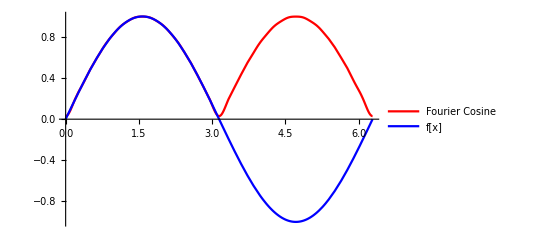

```mathematica
(*Problem #9a plot fourier cosine series of a SINE function*)
Clear[a,b,M,x,n,L,f]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,0,L}]*(2/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,0,L}]*(2/L)
f[x_]:=Sin[Pi*x/L]
L:=Pi

a[n]
b[n]

myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

Plot[{Evaluate[myFCos[x,20]],f[x]},{x,0,2L},PlotRange->f[L],PlotStyle->{Red,Blue},PlotLegends->{"Fourier Cosine","f[x]"}]
```

-(2 n Sin[n π])/((-1+n^2) π)

(2 n (1+Cos[n π]))/((-1+n^2) π)

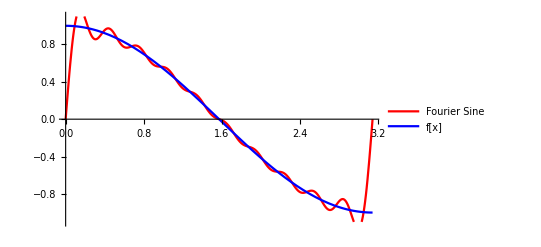

```mathematica
(*Problem #9b plot fourier sine series of a COSINE function*)
Clear[a,b,M,x,n,L,f]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,0,L}]*(2/L)
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,0,L}]*(2/L)
f[x_]:=Cos[Pi*x/L]
L:=Pi

a[n]
b[n]

myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

Plot[{Evaluate[myFSin[x,20]],f[x]},{x,0,L},PlotRange->{-1.1,1.1},PlotStyle->{Red,Blue},PlotLegends->{"Fourier Sine","f[x]"}]
```